#### High-temp Lab

We need to evaluate the resistance_temperature notebook to get the correlation functions we need.

```mathematica
cd = NotebookDirectory[];
NotebookEvaluate[NotebookOpen[
FileNameJoin[{cd, "resistance_temperature.nb"}]
]];
```

```mathematica
NotebookClose[
FileNameJoin[{cd, "resistance_temperature.nb"}]
];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
highTempDataRaw = Import[FileNameJoin[{cd, "data/high-temp.csv"}]]
```

{{V (lamp),V error,I,I error,mV (detector),mV error},{0.,0.005,0.,0.01,0.01,0.005},{0.5,0.005,0.46,0.02,0.11,0.015},{1.,0.001,0.571,0.01,0.16,0.05},{1.5,0.001,0.653,0.01,0.264,0.005},{2.,0.001,0.729,0.01,0.423,0.005},{2.5,0.001,0.8,0.01,0.605,0.008},{3.,0.005,0.868,0.01,0.834,0.005},{3.5,0.001,0.932,0.01,1.1,0.01},{4.,0.001,0.994,0.005,1.43,0.005},{4.5,0.001,1.05,0.005,1.76,0.005},{5.,0.001,1.107,0.005,2.11,0.005},{5.5,0.001,1.161,0.005,2.5,0.005},{6.,0.001,1.214,0.005,2.89,0.005},{6.5,0.001,1.263,0.005,3.34,0.005},{7.,0.001,1.211,0.005,3.83,0.005},{7.5,0.001,1.358,0.005,4.31,0.005},{8.,0.005,1.403,0.005,4.8,0.01}}

```mathematica
lampVoltage= Drop[Transpose[highTempDataRaw][[1]],1];
```

```mathematica
ΔlampVoltage = Drop[Transpose[highTempDataRaw][[2]],1];
```

```mathematica
lampCurrent = Drop[Transpose[highTempDataRaw][[3]],1];
```

```mathematica
ΔlampCurrent = Drop[Transpose[highTempDataRaw][[4]],1];
```

```mathematica
detectorVoltage = Drop[Transpose[highTempDataRaw][[5]],1];
```

```mathematica
ΔdetectorVoltage = Drop[Transpose[highTempDataRaw][[6]],1];
```

We can then calculate the resistance for each of the voltages. Using R = V/I,

```mathematica
lampResistance = lampVoltage/lampCurrent
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,1.08696,1.75131,2.29709,2.74348,3.125,3.45622,3.75536,4.02414,4.28571,4.51671,4.7373,4.94234,5.14648,5.78035,5.52283,5.70207}

and the associated errors:

```mathematica
ΔlampResistance = Table[lampResistance[[i]] Sqrt[
(ΔlampVoltage[[i]]/lampVoltage[[i]])^2 + 
(ΔlampCurrent[[i]]/lampCurrent[[i]])^2], {i, 1, Length[lampVoltage]}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

{Indeterminate,0.0484929,0.0307209,0.0352108,0.0376585,0.0390825,0.0402327,0.0403079,0.0202672,0.0204304,0.0204207,0.02042,0.0203723,0.0203894,0.0238803,0.0203477,0.0206311}

However, the resistance (and its uncertainty) at V=0 are not actually infinity, and can be measured. We can replace the infinities with our measured values, giving

```mathematica
lampResistance[[1]] = 0.586;
ΔlampResistance[[1]] = 0;
```

Since the correlation function takes a resistance ratio instead of the actual resistance, we need to adjust our data to match.

```mathematica
lampResistanceRatio = lampResistance/lampResistance[[1]];
ΔlampResistanceRatio = ΔlampResistance / lampResistance[[1]];
```

Then we can get the temperature of the lamp (and its error)

```mathematica
lampTemp = corrfunc[lampResistanceRatio]
```

{300.,496.642,727.254,907.604,1050.32,1172.34,1276.14,1368.92,1451.5,1530.55,1599.6,1665.74,1726.66,1786.66,1972.05,1897.36,1949.45}

```mathematica
ΔlampTemp = ΔlampResistanceRatio * dcorrfunc[lampResistanceRatio]
```

{0.,18.3918,10.3046,11.4286,11.8816,12.5713,12.4161,12.4909,6.17435,6.12485,6.09515,6.10833,6.00495,5.98216,6.88127,5.95602,5.96779}

Then we need to take the logarithm of these

```mathematica
logLampTemp = Log[lampTemp];
```

```mathematica
ΔlogLampTemp = ΔlampTemp (1/lampTemp);
```

```mathematica
logDetectorVoltage = Log[detectorVoltage];
```

```mathematica
ΔlogDetectorVoltage = ΔdetectorVoltage (1/detectorVoltage);
```

```mathematica
highVOrderedPairs = Table[{logLampTemp[[i]], logDetectorVoltage[[i]]},  {i, 1, Length[logLampTemp]}];
```

```mathematica
highVLinearFit = LinearModelFit[highVOrderedPairs, x, x]
```

FittedModel[-22.2022+3.10703 x]

```mathematica
highVLinearFit["ParameterErrors"]
```

{0.861742,0.120996}

```mathematica
highVErrorPairs = Table[{highVOrderedPairs[[i]], ErrorBar[ΔlogDetectorVoltage[[i]]]}, {i, 1, Length[highVOrderedPairs]}];
```

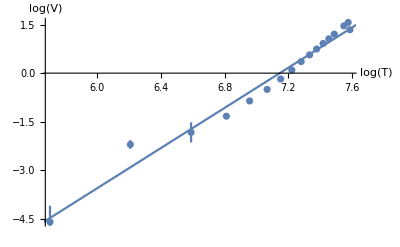

```mathematica
Show[{ErrorListPlot[highVErrorPairs], Plot[highVLinearFit[x], {x, 5, 8}]},AxesLabel->{"log(T)","log(V)"}]
```

#### Low-temp lab

```mathematica
lowTempDataRaw = Import[FileNameJoin[{cd, "data/low-temp.csv"}]]
```

{{T,R,R error,V,V error},{30,79422,200,0.661,0.005},{40,51048,200,1.48,0.005},{50,33591,200,2.2,0.01},{60,22590,100,3.33,0.005},{70,15502,100,4.2,0.01},{80,10837,100,5.44,0.005},{90,7707,100,6.7,0.005},{100,5569,100,8.04,0.005},{110,4070,30,9.53,0.005},{120,2952,50,11.3,0.005}}

```mathematica
cubeTemp = Drop[Transpose[lowTempDataRaw][[1]],1];
```

```mathematica
cubeResistance =Drop[Transpose[lowTempDataRaw][[2]],1];
```

```mathematica
ΔcubeResistance = Drop[Transpose[lowTempDataRaw][[3]],1];
```

```mathematica
detectorVoltage2 = Drop[Transpose[lowTempDataRaw][[4]],1];
```

```mathematica
ΔdetectorVoltage2 = Drop[Transpose[lowTempDataRaw][[5]],1];
```

```mathematica
cubeTempCalculated = corrfunc3[cubeResistance]
```

{303.15,313.15,323.15,333.15,343.15,353.15,363.153,373.152,383.254,394.086}

```mathematica
ΔcubeTempCalculated = ΔcubeResistance *dcorrfunc3[cubeResistance];
```

```mathematica
cubeTemp4 = cubeTempCalculated^4;
```

```mathematica
ΔcubeTemp4 = ΔcubeTempCalculated * (4 cubeTempCalculated^3);
```

```mathematica
lowTempOrderedPairs = Table[{cubeTemp4[[i]], detectorVoltage2[[i]]}, {i, 1, Length[cubeTemp4]}];
```

```mathematica
lowTempErrorPairs = Table[{lowTempOrderedPairs[[i]], ErrorBar[ΔdetectorVoltage2[[i]]]}, {i, 1, Length[lowTempOrderedPairs]}];
```

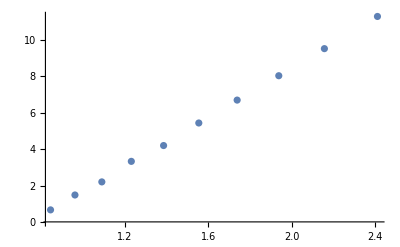

```mathematica
lowTempDataPlot = ErrorListPlot[lowTempErrorPairs]
```

```mathematica
lowTempModel = LinearModelFit[lowTempOrderedPairs, x, x]
```

FittedModel[-5.10767+6.78667×10^-10 x]

```mathematica
lowTempModelPlot = Plot[lowTempModel[x], {x, 0, 3 10^10}];
```

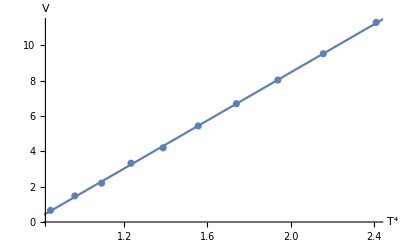

```mathematica
Show[lowTempDataPlot, lowTempModelPlot, AxesLabel-> {"T^4", "V"}]
```

```mathematica
lowTempModel["RSquared"]
```

0.99972

```mathematica
lowTempModel["ParameterErrors"]
```

{0.0647003,4.01699×10^-12}

The room temperature is expected to be

```mathematica
T0[A_,B_] := (-A/B)^(1/4)
```

```mathematica
T0[-5.10767179962723, 6.786668437867565*^-10]
```

294.538

and the error is

```mathematica
T0dA[A_,B_] = D[T0[A,B], A]
```

-1/(4 (-A/B)^(3/4) B)

```mathematica
T0dB[A_,B_] = D[T0[A,B], B]
```

A/(4 (-A/B)^(3/4) B^2)

```mathematica
ΔT0 = Sqrt[(0.06470029254104451 T0dA[-5.10767179962723, 6.786668437867565*^-10])^2 + 
(4.0169880973267945*^-12 T0dB[-5.10767179962723, 6.786668437867565*^-10])^2 ]
```

1.02955